## Harper — PS 11 — 2025-03-18

## EIWL Sections 29, 30

## Section 29

```mathematica
Array[Prime[#]&,100]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97,101,103,107,109,113,127,131,137,139,149,151,157,163,167,173,179,181,191,193,197,199,211,223,227,229,233,239,241,251,257,263,269,271,277,281,283,293,307,311,313,317,331,337,347,349,353,359,367,373,379,383,389,397,401,409,419,421,431,433,439,443,449,457,461,463,467,479,487,491,499,503,509,521,523,541}

```mathematica
Array[Prime[#+1]-Prime[#]&,100]
```

{1,2,2,4,2,4,2,4,6,2,6,4,2,4,6,6,2,6,4,2,6,4,6,8,4,2,4,2,4,14,4,6,2,10,2,6,6,4,6,6,2,10,2,4,2,12,12,4,2,4,6,2,10,6,6,6,2,6,4,2,10,14,4,2,4,14,6,10,2,4,6,8,6,6,4,6,8,4,8,10,2,10,2,6,4,6,8,4,2,4,12,8,4,8,4,6,12,2,18,6}

```mathematica
Grid[Array[#1+#2&,{10,10}]]
```

2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11
3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13
5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14
6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15
7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16
8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17
9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18
10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19
11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20

```mathematica
FoldList[Times,1,Range[10]]
```

{1,1,2,6,24,120,720,5040,40320,362880,3628800}

```mathematica
FoldList[Times,Array[Prime[#]&,10]]
```

{2,6,30,210,2310,30030,510510,9699690,223092870,6469693230}

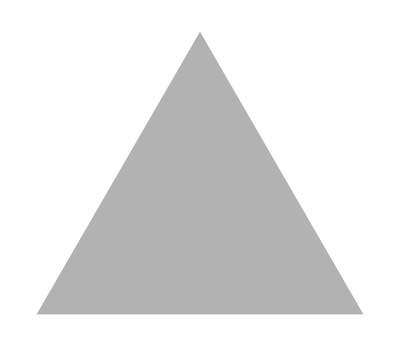
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
FoldList[ImageAdd,Table[Graphics[{Opacity[0.3],RegularPolygon[x]}],{x,3,8}]]
```

## Section 30

```mathematica
Thread[FromLetterNumber[Range[26]]->Range[26]]
```

{a→1,b→2,c→3,d→4,e→5,f→6,g→7,h→8,i→9,j→10,k→11,l→12,m→13,n→14,o→15,p→16,q→17,r→18,s→19,t→20,u→21,v→22,w→23,x→24,y→25,z→26}

```mathematica
Grid[Partition[FromLetterNumber[Range[24]],6]]
```

a | b | c | d | e | f
g | h | i | j | k | l
m | n | o | p | q | r
s | t | u | v | w | x

```mathematica
Grid[Partition[IntegerDigits[2^1000],50],Frame->All]
```

1 | 0 | 7 | 1 | 5 | 0 | 8 | 6 | 0 | 7 | 1 | 8 | 6 | 2 | 6 | 7 | 3 | 2 | 0 | 9 | 4 | 8 | 4 | 2 | 5 | 0 | 4 | 9 | 0 | 6 | 0 | 0 | 0 | 1 | 8 | 1 | 0 | 5 | 6 | 1 | 4 | 0 | 4 | 8 | 1 | 1 | 7 | 0 | 5 | 5
3 | 3 | 6 | 0 | 7 | 4 | 4 | 3 | 7 | 5 | 0 | 3 | 8 | 8 | 3 | 7 | 0 | 3 | 5 | 1 | 0 | 5 | 1 | 1 | 2 | 4 | 9 | 3 | 6 | 1 | 2 | 2 | 4 | 9 | 3 | 1 | 9 | 8 | 3 | 7 | 8 | 8 | 1 | 5 | 6 | 9 | 5 | 8 | 5 | 8
1 | 2 | 7 | 5 | 9 | 4 | 6 | 7 | 2 | 9 | 1 | 7 | 5 | 5 | 3 | 1 | 4 | 6 | 8 | 2 | 5 | 1 | 8 | 7 | 1 | 4 | 5 | 2 | 8 | 5 | 6 | 9 | 2 | 3 | 1 | 4 | 0 | 4 | 3 | 5 | 9 | 8 | 4 | 5 | 7 | 7 | 5 | 7 | 4 | 6
9 | 8 | 5 | 7 | 4 | 8 | 0 | 3 | 9 | 3 | 4 | 5 | 6 | 7 | 7 | 7 | 4 | 8 | 2 | 4 | 2 | 3 | 0 | 9 | 8 | 5 | 4 | 2 | 1 | 0 | 7 | 4 | 6 | 0 | 5 | 0 | 6 | 2 | 3 | 7 | 1 | 1 | 4 | 1 | 8 | 7 | 7 | 9 | 5 | 4
1 | 8 | 2 | 1 | 5 | 3 | 0 | 4 | 6 | 4 | 7 | 4 | 9 | 8 | 3 | 5 | 8 | 1 | 9 | 4 | 1 | 2 | 6 | 7 | 3 | 9 | 8 | 7 | 6 | 7 | 5 | 5 | 9 | 1 | 6 | 5 | 5 | 4 | 3 | 9 | 4 | 6 | 0 | 7 | 7 | 0 | 6 | 2 | 9 | 1
4 | 5 | 7 | 1 | 1 | 9 | 6 | 4 | 7 | 7 | 6 | 8 | 6 | 5 | 4 | 2 | 1 | 6 | 7 | 6 | 6 | 0 | 4 | 2 | 9 | 8 | 3 | 1 | 6 | 5 | 2 | 6 | 2 | 4 | 3 | 8 | 6 | 8 | 3 | 7 | 2 | 0 | 5 | 6 | 6 | 8 | 0 | 6 | 9 | 3

```mathematica
Grid[Partition[Take[Characters[WikipediaData["Computers"]],400],20],Frame->All]
```

A |   | c | o | m | p | u | t | e | r |   | i | s |   | a |   | m | a | c | h
i | n | e |   | t | h | a | t |   | c | a | n |   | b | e |   | p | r | o | g
r | a | m | m | e | d |   | t | o |   | a | u | t | o | m | a | t | i | c | a
l | l | y |   | c | a | r | r | y |   | o | u | t |   | s | e | q | u | e | n
c | e | s |   | o | f |   | a | r | i | t | h | m | e | t | i | c |   | o | r
  | l | o | g | i | c | a | l |   | o | p | e | r | a | t | i | o | n | s |  
( | c | o | m | p | u | t | a | t | i | o | n | ) | . |   | M | o | d | e | r
n |   | d | i | g | i | t | a | l |   | e | l | e | c | t | r | o | n | i | c
  | c | o | m | p | u | t | e | r | s |   | c | a | n |   | p | e | r | f | o
r | m |   | g | e | n | e | r | i | c |   | s | e | t | s |   | o | f |   | o
p | e | r | a | t | i | o | n | s |   | k | n | o | w | n |   | a | s |   | p
r | o | g | r | a | m | s | . |   | T | h | e | s | e |   | p | r | o | g | r
a | m | s |   | e | n | a | b | l | e |   | c | o | m | p | u | t | e | r | s
  | t | o |   | p | e | r | f | o | r | m |   | a |   | w | i | d | e |   | r
a | n | g | e |   | o | f |   | t | a | s | k | s | . |   | T | h | e |   | t
e | r | m |   | c | o | m | p | u | t | e | r |   | s | y | s | t | e | m |  
m | a | y |   | r | e | f | e | r |   | t | o |   | a |   | n | o | m | i | n
a | l | l | y |   | c | o | m | p | l | e | t | e |   | c | o | m | p | u | t
e | r |   | t | h | a | t |   | i | n | c | l | u | d | e | s |   | t | h | e
  | h | a | r | d | w | a | r | e | , |   | o | p | e | r | a | t | i | n | g

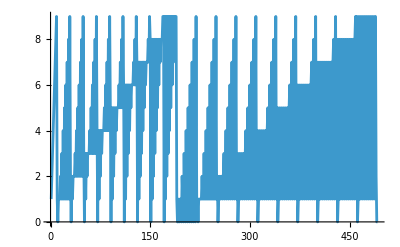

```mathematica
ListLinePlot[Flatten[IntegerDigits[Range[200]]]]
```


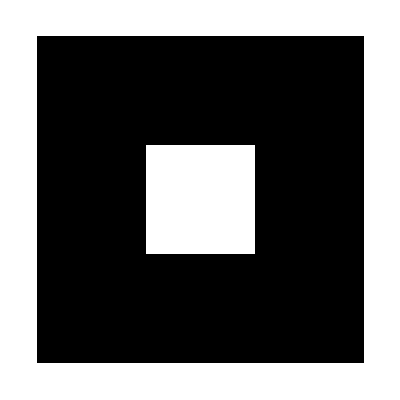
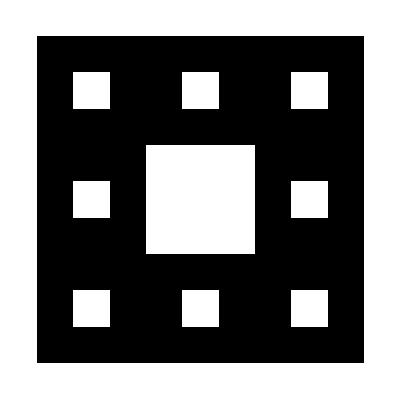
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ArrayPlot/@NestList[ArrayFlatten[{{#,#,#},{#,0,#},{#,#,#}}]&,{{1}},4]
```

```mathematica
Select[Flatten[Table[{x,y,Sqrt[x^2+y^2]},{x,20},{y,20}],1],IntegerQ[Last[#]]&]
```

{{3,4,5},{4,3,5},{5,12,13},{6,8,10},{8,6,10},{8,15,17},{9,12,15},{12,5,13},{12,9,15},{12,16,20},{15,8,17},{15,20,25},{16,12,20},{20,15,25}}

```mathematica
Table[Max[Length[Gather[IntegerDigits[2^n]]]],{n,100}]
```

{1,1,1,2,2,2,3,3,3,4,4,4,4,5,5,3,5,4,4,7,6,5,4,4,4,6,6,6,9,7,7,5,6,6,7,7,8,7,7,7,6,8,7,9,8,7,8,9,7,8,9,8,7,7,8,8,7,9,8,9,9,9,9,9,9,8,9,10,9,10,7,9,8,9,9,9,8,9,10,9,9,10,9,10,9,9,10,10,10,9,8,9,9,10,10,10,10,10,9,10}

```mathematica
GatherBy[Array[IntegerName,100],StringTake[#,1]&]
```

{{one,one hundred},{two,three,ten,twelve,thirteen,twenty,twenty-one,twenty-two,twenty-three,twenty-four,twenty-five,twenty-six,twenty-seven,twenty-eight,twenty-nine,thirty,thirty-one,thirty-two,thirty-three,thirty-four,thirty-five,thirty-six,thirty-seven,thirty-eight,thirty-nine},{four,five,fourteen,fifteen,forty,forty-one,forty-two,forty-three,forty-four,forty-five,forty-six,forty-seven,forty-eight,forty-nine,fifty,fifty-one,fifty-two,fifty-three,fifty-four,fifty-five,fifty-six,fifty-seven,fifty-eight,fifty-nine},{six,seven,sixteen,seventeen,sixty,sixty-one,sixty-two,sixty-three,sixty-four,sixty-five,sixty-six,sixty-seven,sixty-eight,sixty-nine,seventy,seventy-one,seventy-two,seventy-three,seventy-four,seventy-five,seventy-six,seventy-seven,seventy-eight,seventy-nine},{eight,eleven,eighteen,eighty,eighty-one,eighty-two,eighty-three,eighty-four,eighty-five,eighty-six,eighty-seven,eighty-eight,eighty-nine},{nine,nineteen,ninety,ninety-one,ninety-two,ninety-three,ninety-four,ninety-five,ninety-six,ninety-seven,ninety-eight,ninety-nine}}

```mathematica
SortBy[Take[WordList[],50],StringTake[StringReverse[#],1]&]
```

{a,abandoned,abashed,abbreviated,abed,abalone,abase,abate,abbe,abbreviate,abdicate,abeyance,abhorrence,abidance,abide,abducting,abiding,aah,abash,aardvark,aback,abdominal,abeam,abandon,abbreviation,abdication,abdomen,abduction,aberration,abjection,abattoir,abductor,abettor,abhor,abacus,abbess,abaft,abandonment,abasement,abashment,abatement,abbot,abduct,aberrant,abet,abhorrent,abject,abbey,ability,abjectly}

```mathematica
SortBy[Table[n^2,{n,20}],First[IntegerDigits[#]]&]
```

{1,16,100,121,144,169,196,25,225,256,289,36,324,361,4,49,400,64,81,9}

```mathematica
SortBy[Range[20],Length[Characters[IntegerName[#]]]&]
```

{1,2,6,10,4,5,9,3,7,8,11,12,20,15,16,13,14,18,19,17}

```mathematica
GatherBy[RandomSample[WordList[],20],StringLength]
```

{{topple,enough,tanned,sorbet},{amuse},{brushwork,ruination,socialist,frivolous},{transmogrification},{fortuneteller},{valuable,unproved},{exaggerated,coeducation,kitchenware},{curt,oops},{karaoke},{salutation}}

```mathematica
Complement[Alphabet["Ukrainian"],Alphabet["Russian"]]
```

{є,і,ї,ґ}

```mathematica
Intersection[Table[n^2,{n,100}],Table[n^3,{n,100}]]
```

{1,64,729,4096}

```mathematica
Intersection[EntityList[],EntityList[]]
```

{Canada,France,Germany,Italy,United Kingdom,United States}

```mathematica
Grid[Transpose[Permutations[Range[4]]]]
```

1 | 1 | 1 | 1 | 1 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 4 | 4 | 4 | 4
2 | 2 | 3 | 3 | 4 | 4 | 1 | 1 | 3 | 3 | 4 | 4 | 1 | 1 | 2 | 2 | 4 | 4 | 1 | 1 | 2 | 2 | 3 | 3
3 | 4 | 2 | 4 | 2 | 3 | 3 | 4 | 1 | 4 | 1 | 3 | 2 | 4 | 1 | 4 | 1 | 2 | 2 | 3 | 1 | 3 | 1 | 2
4 | 3 | 4 | 2 | 3 | 2 | 4 | 3 | 4 | 1 | 3 | 1 | 4 | 2 | 4 | 1 | 2 | 1 | 3 | 2 | 3 | 1 | 2 | 1

```mathematica
StringJoin/@Permutations[Characters["hello"]]
```

{hello,helol,heoll,hlelo,hleol,hlleo,hlloe,hloel,hlole,hoell,holel,holle,ehllo,ehlol,eholl,elhlo,elhol,ellho,elloh,elohl,elolh,eohll,eolhl,eollh,lhelo,lheol,lhleo,lhloe,lhoel,lhole,lehlo,lehol,lelho,leloh,leohl,leolh,llheo,llhoe,lleho,lleoh,llohe,lloeh,lohel,lohle,loehl,loelh,lolhe,loleh,ohell,ohlel,ohlle,oehll,oelhl,oellh,olhel,olhle,olehl,olelh,ollhe,olleh}

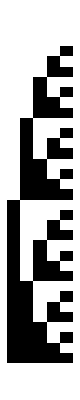

```mathematica
ArrayPlot[Tuples[{0,1},5]]
```

```mathematica
Table[StringJoin[RandomSample[FromLetterNumber[Range[26]],5]],10]
```

{gilwe,kynjh,btdsv,hwkxp,lofap,zbdtx,xcsrf,xecam,jwybz,wqzfe}

```mathematica
Tuples[{1,2},3]
```

{{1,1,1},{1,1,2},{1,2,1},{1,2,2},{2,1,1},{2,1,2},{2,2,1},{2,2,2}}